```mathematica
(* Sample Cauchy Distributions *)

Clear[x0, γ,y0,δ] ;
X= CauchyDistribution[x0,γ] ;
Y= CauchyDistribution[y0,δ] ;
Z = CauchyDistribution[x0+y0, δ+γ] ;

PDF[X,x]
PDF[Y,x]
PDF[Z,x]
```

1/(π (1+(x-x0)^2/γ^2) γ)

1/(π (1+(x-y0)^2/δ^2) δ)

1/(π (γ+δ) (1+(x-x0-y0)^2/(γ+δ)^2))

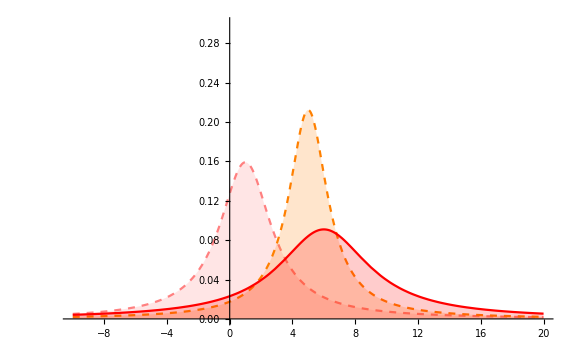

```mathematica
x0 = 1;
y0 = 5;
γ =2;
δ = 1.5;

Show[
Plot[PDF[X,x]//Evaluate,{x,-10,20},Filling->Axis, PlotRange->{All,{0,0.3}}, PlotStyle->{Dashed, Pink}],
Plot[PDF[Y,x]//Evaluate,{x,-10,20},Filling->Axis,  PlotRange->{All,{0,0.3}},  PlotStyle->{Dashed, Orange}],
Plot[PDF[Z,x]//Evaluate,{x,-10,20},Filling->Axis,  PlotRange->{All,{0,0.3}},   PlotStyle->{Red}],
ImageSize-> Large
]
```

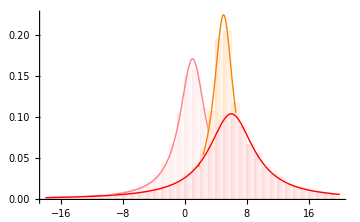

```mathematica
dataX=RandomVariate[ X,10^4] ;
dataY=RandomVariate[ Y,10^4];
dataZ=RandomVariate[ Z,10^4];
Show[
Histogram[dataX,{-18,20,1},PDF, ChartStyle->LightPink, ChartElementFunction->"FadingRectangle"],
Plot[PDF[TruncatedDistribution[{-18,20},X],x],{x,-18,20},PlotStyle->{Pink, Thick}, PlotRange->{All,{0,0.3}}],

Histogram[dataY,{-18,20,1},PDF, ChartStyle->LightOrange, ChartElementFunction->"FadingRectangle"],
Plot[PDF[TruncatedDistribution[{-18,20},Y],x],{x,-18,20},PlotStyle->{Orange, Thick}, PlotRange->{All,{0,0.3}}],

Histogram[dataZ,{-18,20,1},PDF, ChartStyle->LightRed, ChartElementFunction->"FadingRectangle"],
Plot[PDF[TruncatedDistribution[{-18,20},Z],x],{x,-18,20},PlotStyle->{Red, Thick}, PlotRange->{All,{0,0.3}}],
ImageSize-> Medium
]
```

```mathematica
(* Characteristic functions of the above *)

Clear[x0,y0,γ,δ]
Integrate[ ⅇ^(ⅈ*t*x)*PDF[X,x], {x, -Infinity, Infinity}, Assumptions->{Im[t]==0, Im[γ]==0, Im[x0]==0,  γ>0, t>0}]
Integrate[ ⅇ^(ⅈ*t*x)*PDF[Y,x], {x, -Infinity, Infinity}, Assumptions->{Im[t]==0, Im[δ]==0, Im[y0]==0, δ>0, t>0}]
Integrate[ ⅇ^(ⅈ*t*x)*PDF[Z,x], {x, -Infinity, Infinity}, 
Assumptions->{Im[t]==0, Im[δ]==0,Im[γ]==0, Im[x0]==0, Im[y0]==0,  γ>0, δ>0, t>0}]
```

ⅇ^(ⅈ t x0-t γ)

ⅇ^(ⅈ t y0-t δ)

ⅇ^(ⅈ t (x0+y0+ⅈ (γ+δ)))

```mathematica
(* STABILITY LAW *)
```

```mathematica
Integrate[ ⅇ^(ⅈ*t*x)*(PDF[X,x]+ PDF[Y,x]), {x, -Infinity, Infinity}, 
Assumptions->{Im[t]==0, Im[δ]==0,Im[γ]==0, Im[x0]==0, Im[y0]==0,  γ>0, δ>0, t>0}]
```

ⅇ^(ⅈ t x0-t γ)+ⅇ^(ⅈ t y0-t δ)